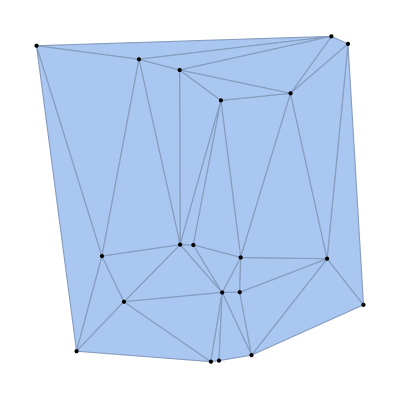

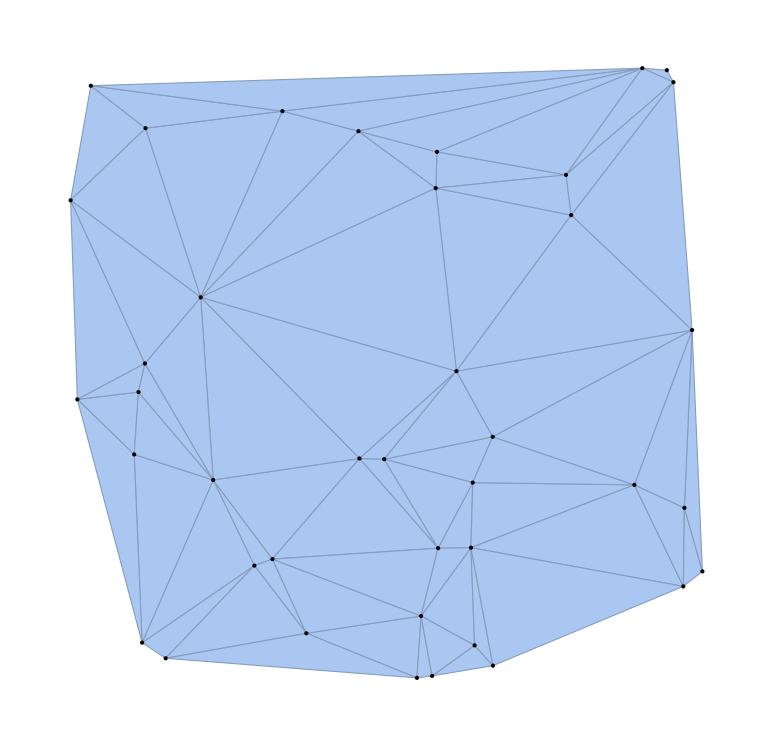

```mathematica
pts1=RandomReal[{-1,1},{20,2}];
pts2 =RandomReal[{-1,1},{20,2}];
ℛ=DelaunayMesh[pts1];
HighlightMesh[ℛ,Style[0,Black]]
ℛ=DelaunayMesh[Join[pts1, pts2]];
HighlightMesh[ℛ,Style[0,Black]]
```